Doing α= 0

So Q is:   1

Doing α= 0.02

So Q is:   50

Doing α= 0.04

So Q is:   25

Doing α= 0.06

So Q is:   50

Doing α= 0.08

So Q is:   25

Doing α= 0.1

So Q is:   10

Doing α= 0.12

So Q is:   25

Doing α= 0.14

So Q is:   50

Doing α= 0.16

So Q is:   25

Doing α= 0.18

So Q is:   50

Doing α= 0.2

So Q is:   5

Doing α= 0.22

So Q is:   50

Doing α= 0.24

So Q is:   25

Doing α= 0.26

So Q is:   50

Doing α= 0.28

So Q is:   25

Doing α= 0.3

So Q is:   10

Doing α= 0.32

So Q is:   25

Doing α= 0.34

So Q is:   50

Doing α= 0.36

So Q is:   25

Doing α= 0.38

So Q is:   50

Doing α= 0.4

So Q is:   5

Doing α= 0.42

So Q is:   50

Doing α= 0.44

So Q is:   25

Doing α= 0.46

So Q is:   50

Doing α= 0.48

So Q is:   25

Doing α= 0.5

So Q is:   2

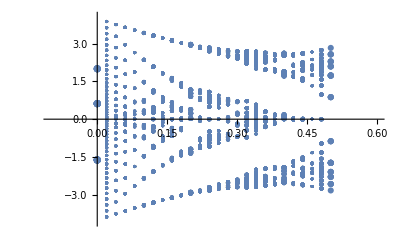

```mathematica
Begin["Pr1`"];
ClearAll["Pr1`*"];

t=1.;
Ncellsy=5;
Ncellsx=5;
αlist={0,0.02, 0.04, 0.06, 0.08, 0.1, 0.12, 0.14, 0.16, 0.18, 0.2, 0.22, 0.24, 0.26, 0.28, 0.3, 0.32, 0.34, 0.36, 0.38, 0.4, 0.42, 0.44, 0.46, 0.48, 0.5}; (* Denser for nice butterfly, but beware: it will take time! *)
Qlist={};
En={};


For[kk=1, kk<Length[αlist]+1, kk++,
α=αlist[[kk]];
Q=If[α>0,Denominator[Rationalize[α]], 1];
Print["Doing α= " , α];
Print["So Q is:   " , Q];
Qlist=Append[Qlist, Q];
If[Q>2,   MM=With[{Nn=N[Q], pattern={t,t}},SparseArray[{Band[{1,2},{-2,-1}]->pattern,Band[{2,1},{-1,-2}]->pattern},{Nn,Nn}]],   
If[Q==2, MM=SparseArray[{{1,2}->t,{2,1}->t}], MM={{0}}   ] ]    ;
MM=Normal[MM];
Enα={};
For[m=1, m<Ncellsy+1, m++,  ky=2*π/Ncellsy*m;
For[n=1,  n<Ncellsx+1, n++, kx=2*π/(Q* Ncellsx)*n; 
Matrix=Table[MM[[i]][[j]],{i,Q},{j,Q}];
Matrix[[1]][[Q]]=Matrix[[1]][[Q]]+t*N[ⅇ^(-ⅈ*Q*kx)];
Matrix[[Q]][[1]]=Matrix[[Q]][[1]]+t*N[ⅇ^(+ⅈ*Q*kx)];
For[q=1, q<Q+1, q++,  Matrix[[q]][[q]]=2*t*N[Cos[ky-2*π*α*q]] ];
(* Print[MatrixForm[Matrix]];  *)

If[ Q>1,   Enα=Append[Enα, Eigenvalues[Matrix]], Enα=Append[Enα, {Matrix[[1]][[1]]}]  ];

];
];

En=Append[En, Enα];
]
En  ;
Maxx=Max[En];
Minn=Min[En];


plotEn[x_, kk_, m_, n_, q_]:= En[[kk]][[(m-1) *Ncellsx+n]][[q]]   ;
(*  
Show[
Table[ Table[  Plot[ plotEn[x, kk, m, n, q], {x, αlist[[kk]]-0.01, αlist[[kk]]+0.01}, PlotRange->{{-0.1, 0.6},{Minn-0.2, Maxx+0.2}}],  {m,  Ncellsy}, {n,  Ncellsx}, {q, Qlist[[kk]]}] ,{kk,  Length[αlist]}]

] *)



Enb={};
For[kk=1, kk<Length[αlist]+1, kk++,
   Enbα={};
For[m=1,m<Ncellsy+1, m++,
For[n=1,n<Ncellsx+1, n++,
For[q=1,q<Qlist[[kk]]+1, q++,
Enbα=Append[Enbα,  { αlist[[kk]] ,En[[kk]][[(m-1) *Ncellsx+n]][[q]]   } ];
];
];
];
Enb=Append[Enb,  Enbα ];
];

Show[
Table[ListPlot[Enb[[kk]], PlotRange->{{-0.1, 0.6},{Minn-0.2, Maxx+0.2}}   ], {kk,  Length[αlist]} ]
]
```